In cellulose Iβ crystal, (b->c), (c->b), (k->l), (l->k), (β->γ), (γ->β)

#### Monoclinic

```mathematica
ClearAll["Global`*"]
λ=1.5418;(*Kα1&Kα2*)
calc[h_,k_,l_,α_,β_,γ_,a_,b_,c_]:=Module[{},
(* d=(a b c)/(√(a^2 c^2 k^2-2 a b^2 c h l Cot[° β] Csc[° β]+b^2 c^2 h^2 Csc[° β]^2+a^2 b^2 l^2 Csc[° β]^2)) *)
(* In cellulose Iβ crystal, (b->c), (c->b), (k->l), (l->k), (β->γ), (γ->β) *)
d=(a b c)/(√(a^2 b^2 l^2-2 a c^2 b h k Cot[° γ] Csc[° γ]+c^2 b^2 h^2 Csc[° γ]^2+a^2 c^2 k^2 Csc[° γ]^2));(*β here is γ in cellulose Iβ crystal*)
θ=ArcSin[λ/(2d)]*180/π;
];
```

```mathematica
calc[1,1,0,90,90,96.5,7.784,8.201,10.380];
Print["2θ(110)= ",Round[2θ,0.1], ", d(110)= ",d]

calc[1,-1,0,90,90,96.5,7.784,8.201,10.380];
Print["2θ(1-10)= ",Round[2θ,0.1], ", d(1-10)= ",d]

calc[2,0,0,90,90,96.5,7.784,8.201,10.380];
Print["2θ(200)= ",Round[2θ,0.1],", d(200)= ",d]

calc[0,0,4,90,90,96.5,7.784,8.201,10.380];
Print["2θ(004)= ",Round[2θ,0.1],", d(004)= ",d]
```

2θ(110)= 16.7, d(110)= 5.317

2θ(1-10)= 14.9, d(1-10)= 5.95626

2θ(200)= 23., d(200)= 3.86698

2θ(004)= 34.6, d(004)= 2.595

```mathematica
(*lattice 'a' dependence*)
temp=7.784;
t110={};(*110*)
t110b={};(*1-10*)
t200={};(*200*)
n=Table[temp+i,{i,-1,1,0.1}];
For[j=1,j<=Length[n],j++,
{h,k,l}={1,1,0};
calc[h,k,l,90,90,96.5,n[[j]],8.201,10.380];
AppendTo[t110,2θ];
{h,k,l}={1,-1,0};
calc[h,k,l,90,90,96.5,n[[j]],8.201,10.380];
AppendTo[t110b,2θ];
{h,k,l}={2,0,0};
calc[h,k,l,90,90,96.5,n[[j]],8.201,10.380];
AppendTo[t200,2θ];
]
tta2=Table[{n[[j]],t110[[j]],t110b[[j]],t200[[j]]},{j,1,Length[n]}];
```

```mathematica
(*lattice 'b' dependence*)
temp=8.201;
t110={};(*110*)
t110b={};(*1-10*)
t200={};(*200*)
n=Table[temp+i,{i,-1,1,0.1}];
For[j=1,j<=Length[n],j++,
{h,k,l}={1,1,0};
calc[h,k,l,90,90,96.5,7.784,n[[j]],10.380];
AppendTo[t110,2θ];
{h,k,l}={1,-1,0};
calc[h,k,l,90,90,96.5,7.784,n[[j]],10.380];
AppendTo[t110b,2θ];
{h,k,l}={2,0,0};
calc[h,k,l,90,90,96.5,7.784,n[[j]],10.380];
AppendTo[t200,2θ];
]
ttb2=Table[{n[[j]],t110[[j]],t110b[[j]],t200[[j]]},{j,1,Length[n]}];
```

```mathematica
(*lattice 'γ' dependence*)
temp=96.5;
t110={};(*110*)
t110b={};(*1-10*)
t200={};(*200*)
n=Table[temp+i,{i,-10,10,1}];
For[j=1,j<=Length[n],j++,
{h,k,l}={1,1,0};
calc[h,k,l,90,90,n[[j]],7.784,8.201,10.380];
AppendTo[t110,2θ];
{h,k,l}={1,-1,0};
calc[h,k,l,90,90,n[[j]],7.784,8.201,10.380];
AppendTo[t110b,2θ];
{h,k,l}={2,0,0};
calc[h,k,l,90,90,n[[j]],7.784,8.201,10.380];
AppendTo[t200,2θ];
]
ttg2=Table[{n[[j]],t110[[j]],t110b[[j]],t200[[j]]},{j,1,Length[n]}];
```

#### plotting

```mathematica
p1=ListLinePlot[{
Table[{tta2[[i,1]],tta2[[i,2]]},{i,1,Length[n]}],
Table[{tta2[[i,1]],tta2[[i,3]]},{i,1,Length[n]}],
Table[{tta2[[i,1]],tta2[[i,4]]},{i,1,Length[n]}]},
GridLines->{{7.784}, None},Frame->True,
FrameLabel->{
Style["a (Å)",FontSize->16,Black,Bold],
Style["2θ (°)",FontSize->16,Black,Bold]
},
(*PlotLabel->Style[None,Bold,FontSize->16,Black],*)
FrameStyle->Black,
PlotRange->{All,{13,27}},
FrameTicksStyle->Directive[Black,FontSize->16],
PlotStyle->{Thickness[0.008],Thickness[0.008],Thickness[0.008]} ,
PlotLegends->Placed[SwatchLegend[{"(110)",Style[Row[{"(0",Overscript["1","-"],"0)"}],FontSize->16],Style[Row[{"(2",Overscript["0",""],"0)"}],FontSize->16]},LabelStyle->{FontSize->16,Bold,Black}],{0.15,0.51}],
ImageSize->Medium,AspectRatio->0.9
];
```

```mathematica
p2=ListLinePlot[{
Table[{ttb2[[i,1]],ttb2[[i,2]]},{i,1,Length[n]}],
Table[{ttb2[[i,1]],ttb2[[i,3]]},{i,1,Length[n]}],
Table[{ttb2[[i,1]],ttb2[[i,4]]},{i,1,Length[n]}]},
GridLines->{{8.201}, None},Frame->True,
FrameLabel->{
Style["b (Å)",FontSize->16,Black,Bold],
Style["2θ (°)",FontSize->16,Black,Bold]
},
(*PlotLabel->Style[None,Bold,FontSize->16,Black],*)
FrameStyle->Black,
PlotRange->{All,{13,27}},
FrameTicksStyle->Directive[Black,FontSize->16],
PlotStyle->{Thickness[0.008],Thickness[0.008],Thickness[0.008]} ,
PlotLegends->Placed[SwatchLegend[{"(110)",Style[Row[{"(0",Overscript["1","-"],"0)"}],FontSize->16],Style[Row[{"(2",Overscript["0",""],"0)"}],FontSize->16]},LabelStyle->{FontSize->16,Bold,Black}],{0.15,0.51}],
ImageSize->Medium,AspectRatio->0.9
];
```

```mathematica
p3=ListLinePlot[{
Table[{ttg2[[i,1]],ttg2[[i,2]]},{i,1,Length[n]}],
Table[{ttg2[[i,1]],ttg2[[i,3]]},{i,1,Length[n]}],
Table[{ttg2[[i,1]],ttg2[[i,4]]},{i,1,Length[n]}]},
GridLines->{{96.5}, None},Frame->True,
FrameLabel->{
Style["γ (°)",FontSize->16,Black,Bold],
Style["2θ (°)",FontSize->16,Black,Bold]
},
(*PlotLabel->Style[None,Bold,FontSize->16,Black],*)
FrameStyle->Black,
PlotRange->{All,{13,27}},
FrameTicksStyle->Directive[Black,FontSize->16],
PlotStyle->{Thickness[0.008],Thickness[0.008],Thickness[0.008]} ,
PlotLegends->Placed[SwatchLegend[{"(110)",Style[Row[{"(0",Overscript["1","-"],"0)"}],FontSize->16],Style[Row[{"(2",Overscript["0",""],"0)"}],FontSize->16]},LabelStyle->{FontSize->16,Bold,Black}],{0.15,0.51}],
ImageSize->Medium,AspectRatio->0.9
];
```

#### plot

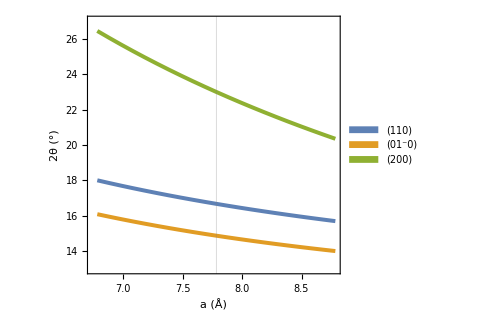
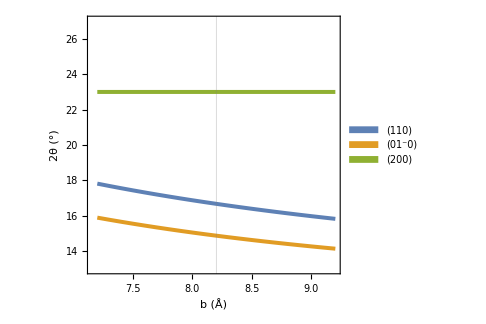
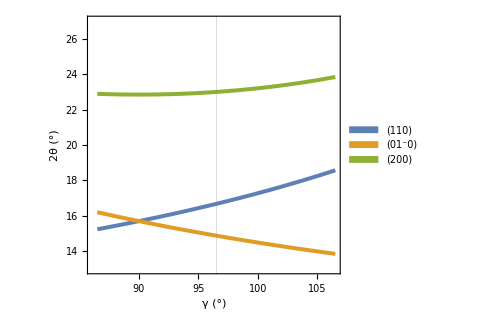

```mathematica
{p1,p2,p3}
```

## Storage

-Graphics-

Nishiyama 2022. J. AM. CHEM. SOC. 2002, 124, 9074-9082